## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
RuleEigenApprox={λ->l (l+1)-s (s+1)};
RuleNearApprox={x^(n_.) (ω̄)^(m_.)->0,x^(n_.) (Ω̄)^(m_.)->0,x^(n_.) χ^(m_.)->0};
RuleFarApprox={n_. x+τ:>n x,n_. x+y_:>n x/;FreeQ[y,x]};
RuleAbsorbC={a_ C[i_]:>C[Unique[]]/;FreeQ[a,x]};
RuleFuncExpansion=
{LegendreP[ν_,μ_,z_]:>((z+1)/(z-1))^(μ/2) Hypergeometric2F1[-ν,ν+1,1-μ,(1-z)/2]};
```

```mathematica
RuleNegativeΓ={Gamma[l α_.+β_.]/Gamma[l γ_.+σ_.]:>(γ (-1)^(l γ+σ-l α-β) Gamma[-l γ-σ+1])/(α Gamma[-l α-β+1])/;Negative[α]&&Negative[γ]};
RuleExtraΓ={Gamma[2+l+x_]/Gamma[1-l+x_]:>((-1)^(l+1) (l+1) x (k^2-x^2)k1l)/l};
```

```mathematica
Subscript[𝔇, x_,n_][r_]:=D[#1, x]-((ⅈ 𝒦[r]) #1)/Δ[r]+((2 n (r-M)) #1)/Δ[r]&;

SuperDagger[(Subscript[𝔇, x_,n_])][r_]:=D[#1, x]+((ⅈ 𝒦[r]) #1)/Δ[r]+((2 n (r-M)) #1)/Δ[r]&;
Subscript[𝔏, y_,n_][θ_]:=D[#1, y]-𝒬[θ] #1+n Cot[θ] #1&;
SuperDagger[(Subscript[𝔏, y_,n_])][θ_]:=D[#1, y]+𝒬[θ] #1+n Cot[θ] #1&;
```

```mathematica
EqTeukolskyRadial//Simplify
```

-λ R[x]+(κ (κ-ⅈ s (2 x+τ)) R[x])/(x (x+τ))+4 ⅈ s (1+x) ω̄ R[x]+(1+s) (2 x+τ) R'[x]+x (x+τ) R''[x]

## Near-horizon approximation ω̄ x≪1 (also Ω̄ x≪1 and χ x≪1)

```mathematica
Eq1 = (EqTeukolskyRadial/.RuleKRadial//Together@*Expand)/. RuleNearApprox // Collect[#, {R[_],Derivative[__][R][_]}, FullSimplify] &
```

((-x λ (x+τ)-ⅈ s τ χ+χ^2) R[x])/(x (x+τ))+(1+s) (2 x+τ) R'[x]+x (x+τ) R''[x]

```mathematica
Sol1=(R[x]/.First[DSolve[Eq1==0,R,x]]//FullSimplify[#1,{{l,s}∈Integers,l≥0}]&)/.RuleFuncExpansion//ExpandAll//FullSimplify//Expand//PowerExpand
```

x^(-s-(ⅈ χ)/τ) (x+τ)^((ⅈ χ)/τ) C[1] Hypergeometric2F1[1/2 (1-√((1+2 s)^2+4 λ)),1/2 (1+√((1+2 s)^2+4 λ)),1-s-(2 ⅈ χ)/τ,-x/τ]+x^(-s/2) (x+τ)^(-s/2) C[2] LegendreQ[1/2 (-1+√((1+2 s)^2+4 λ)),s+(2 ⅈ χ)/τ,1+(2 x)/τ]

```mathematica
EqH=Eq1/(x^α(x+τ)^β)/.{R->Function[x,x^α(x+τ)^β H[x]]}//FullSimplify//Collect[Expand@#,{x^(_.) Derivative[_][H][x],(x^(_.) H[x])/(x (x+τ))},FullSimplify]&
```

((x (α+β) (1+2 s+α+β)-x λ+(α+3 s α+2 α^2+β+s β+2 α β-λ) τ) H[x])/(x+τ)+((α (s+α) τ^2-ⅈ s τ χ+χ^2) H[x])/(x (x+τ))+2 x (1+s+α+β) H'[x]+(1+s+2 α) τ H'[x]+x^2 H''[x]+x τ H''[x]

```mathematica
SolβH=Equal@@(Coefficient[Coefficient[Simplify@ExpandAll[EqH x(x+τ)],H[x]],#]&/@{x^2,x τ})//First@DeleteCases[Solve[#,β],{β->α}]&;
SolαH=Coefficient[Simplify@ExpandAll[(x (x+τ))/H[x] EqH/.SolβH],x,0]//Expand@Solve[#==0,α]&;
SolαβH=Join[#,SolβH/.#]&/@SolαH
```

{{α→-s-(ⅈ χ)/τ,β→(ⅈ χ)/τ},{α→(ⅈ χ)/τ,β→-s-(ⅈ χ)/τ}}

```mathematica
{EqH1,EqH2}=EqH/.SolαβH//Collect[#,{H[_],Derivative[_][H][x]},Cancel@*Simplify]&
```

{(-s-s^2-λ) H[x]+(2 x+τ-s τ-2 ⅈ χ) H'[x]+x (x+τ) H''[x],(-s-s^2-λ) H[x]+(2 x+τ+s τ+2 ⅈ χ) H'[x]+x (x+τ) H''[x]}

```mathematica
Hypergeometric2F1[a,b,c,x]==Hypergeometric2F1[b,a,c,x]
```

True

```mathematica
SolABC=FullSimplify[First@Solve[{a+b+1==Coefficient[#,x H'[x]],a b==Coefficient[#,H[x]],c τ ==Coefficient[#,H'[x]]/.x->0},{a,b,c}]/.RuleEigenApprox,l>0]&/@{EqH1,EqH2}
```

{{a→-l,b→1+l,c→1-s-(2 ⅈ χ)/τ},{a→-l,b→1+l,c→1+s+(2 ⅈ χ)/τ}}

```mathematica
SolNfull= x^α(x+τ)^β Hypergeometric2F1[a,b,c,-x/τ]/.Join@@@Transpose[{SolαβH,SolABC}]//Simplify
```

{x^(-s-(ⅈ χ)/τ) (x+τ)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2 ⅈ χ)/τ,-x/τ],x^((ⅈ χ)/τ) (x+τ)^(-s-(ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1+s+(2 ⅈ χ)/τ,-x/τ]}

```mathematica
SolNear={𝒜 ,0}.SolNfull
```

x^(-s-(ⅈ χ)/τ) 𝒜 (x+τ)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2 ⅈ χ)/τ,-x/τ]

## Far-horizon approximation x≫τ

```mathematica
Eq2=ExpandAll[FullSimplify[EqTeukolskyRadial/x^2]/.RuleKRadial//.RuleFarApprox]/.{a_ x^n_:>0/;n≤-3}//Collect[Simplify[#*x^2],{R[x],R'[x],R''[x]}]&
```

(-λ+2 ⅈ s x ω̄+x^2 (ω̄)^2) R[x]+2 (1+s) x R'[x]+x^2 R''[x]

```mathematica
EqG=Eq2/(x^α Exp[ζ I x ω̄])/.{R->Function[x,x^α Exp[ζ I x ω̄]G[x]]}//FullSimplify//Collect[#/x/.ζ^2->1,Derivative[n_.][G][x],Simplify@*Expand]&
```

(G[x] (α+2 s α+α^2-λ+2 ⅈ x (s+ζ+s ζ+α ζ) ω̄))/x+2 (1+s+α+ⅈ x ζ ω̄) G'[x]+x G''[x]

```mathematica
SolαG=Solve[Coefficient[EqG,G[x]/x]==0/.x->0,α]/.RuleEigenApprox//FullSimplify[#,l> 0]&
```

{{α→-1-l-s},{α→l-s}}

```mathematica
{EqG1,EqG2}=Eq2/.SolαG/.RuleEigenApprox//FullSimplify
```

{(-l (1+l)+s+s^2+x ω̄ (2 ⅈ s+x ω̄)) R[x]+x (2 (1+s) R'[x]+x R''[x]),(-l (1+l)+s+s^2+x ω̄ (2 ⅈ s+x ω̄)) R[x]+x (2 (1+s) R'[x]+x R''[x])}

```mathematica
SolFfull=x^α Exp[ζ I ω̄ x]Hypergeometric1F1[(1+α+s)+ζ s,2(1+s+α),-2 ⅈ ζ x ω̄]/.SolαG
```

{ⅇ^(ⅈ x ζ ω̄) x^(-1-l-s) Hypergeometric1F1[-l+s ζ,-2 l,-2 ⅈ x ζ ω̄],ⅇ^(ⅈ x ζ ω̄) x^(l-s) Hypergeometric1F1[1+l+s ζ,2 (1+l),-2 ⅈ x ζ ω̄]}

```mathematica
SolFar=SolFfull.{𝒟,𝒞}/.ζ->-1
```

ⅇ^(-ⅈ x ω̄) x^(-1-l-s) 𝒟 Hypergeometric1F1[-l-s,-2 l,2 ⅈ x ω̄]+ⅇ^(-ⅈ x ω̄) x^(l-s) 𝒞 Hypergeometric1F1[1+l-s,2 (1+l),2 ⅈ x ω̄]

```mathematica
(Eq2/.{R->Function[x,SolFar//Evaluate]}//FullSimplify)/.ζ^2->1
```

ⅇ^(-ⅈ x ω̄) x^(-1-l-s) (l+l^2-s (1+s)-λ) (𝒟 Hypergeometric1F1[-l-s,-2 l,2 ⅈ x ω̄]+x^(1+2 l) 𝒞 Hypergeometric1F1[1+l-s,2 (1+l),2 ⅈ x ω̄])

## Matching of coefficients

```mathematica
SolNearSeriesFar=SolNear//Normal@Series[#/.{x+τ->x},{x,∞,0}]&//Collect[#,x^_,FullSimplify]&
```

(x^(-1-l-s) 𝒜 (1/τ)^(-1-l) Gamma[-1-2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[-l] Gamma[-((l+s) τ+2 ⅈ χ)/τ])+(2^(-1+2 l) x^(-1+l-s) 𝒜 (1/τ)^(-1+l) Gamma[1/2+l] Gamma[1-s-(2 ⅈ χ)/τ])/(√π Gamma[l-s-(2 ⅈ χ)/τ])+(x^(l-s) 𝒜 (1/τ)^l Gamma[1+2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[1+l] Gamma[1+l-s-(2 ⅈ χ)/τ])

```mathematica
SolFarSeriesNear=SolFar//Normal@Series[#,{x,0,1}]&//Collect[ExpandAll@#,x]&
```

x^(l-s) 𝒞+x^(-1-l-s) 𝒟-(ⅈ s x^(1+l-s) 𝒞 ω̄)/(1+l)+(ⅈ s x^(-l-s) 𝒟 ω̄)/l

```mathematica
EqsCoefFarNear= SolNearSeriesFar-SolFarSeriesNear//Coefficient[(ExpandAll@#)/.{x^(-1-l-s)->𝒰,x^(l-s)->𝒱},{𝒰,𝒱}]&
```

{-𝒟+(𝒜 (1/τ)^(-1-l) Gamma[-1-2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[-l] Gamma[-l-s-(2 ⅈ χ)/τ]),-𝒞+(𝒜 (1/τ)^l Gamma[1+2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[1+l] Gamma[1+l-s-(2 ⅈ χ)/τ])}

```mathematica
RuleMatching=EqsCoefFarNear//PowerExpand@First@Solve[Eliminate[Thread[#==0/.{𝒞->1}],𝒜],𝒟]/.RuleNegativeΓ&
```

{𝒟→((-1)^(1+l) τ^(1+2 l) Gamma[1+l]^2 Gamma[1+l-s-(2 ⅈ χ)/τ])/(2 Gamma[1+2 l] Gamma[2+2 l] Gamma[-l-s-(2 ⅈ χ)/τ])}

## Power at infinity

```mathematica
SolFarSeriesFar=SolFar//Normal@Series[#,{x,∞,0}]&//Collect[ExpandAll@#,{Exp[_] x^-1,Exp[_] x^(-1-2s)},(Simplify[#]/.{Exp[_] x^-2->0}&)]&
```

(ⅇ^(-ⅈ x ω̄) ((2^(-1-l+s) 𝒞 Gamma[2+2 l] (-ⅈ ω̄)^(-1-l+s))/Gamma[1+l+s]+(2^(l+s) 𝒟 Gamma[-2 l] (-ⅈ ω̄)^(l+s))/Gamma[-l+s]))/x+2^(-1-l-s) ⅇ^(ⅈ x ω̄) x^(-1-2 s) ((2^(1+2 l) 𝒟 Gamma[-2 l] (ⅈ ω̄)^(2 l))/Gamma[-l-s]-(ⅈ 𝒞 Gamma[2+2 l])/(Gamma[1+l-s] ω̄)) (ⅈ ω̄)^(-l-s)

```mathematica
{Ain,Aout}=SolFarSeriesFar//Coefficient[#,{ⅇ^(-ⅈ x ω̄) x^-1,ⅇ^(ⅈ x ω̄) x^(-1-2 s)}].DiagonalMatrix[{rp,rp^(1+2s)}]&
```

{rp ((2^(l+s) 𝒟 Gamma[-2 l] (-ⅈ ω̄)^(l+s))/Gamma[-l+s]+(ⅈ 2^(-1-l+s) 𝒞 Gamma[2+2 l] (-ⅈ ω̄)^(-l+s))/(Gamma[1+l+s] ω̄)),rp^(1+2 s) ((2^(l-s) 𝒟 Gamma[-2 l] (ⅈ ω̄)^(l-s))/Gamma[-l-s]-(ⅈ 2^(-1-l-s) 𝒞 Gamma[2+2 l] (ⅈ ω̄)^(-l-s))/(Gamma[1+l-s] ω̄))}

```mathematica
((-1)^(l+1)Gamma[l+2])/(4 (ω̄)^2 Gamma[l])Aout/(rp^(2s)Ain)//.RuleMatching∪{𝒞->1,s->-1}∪RuleNegativeΓ//Together//PowerExpand//Simplify[#,l∈Integers]&
```

(2 Gamma[1+2 l]^2 Gamma[2+2 l]^2 Gamma[1-l-(2 ⅈ χ)/τ]+4^l Gamma[l] Gamma[1+l]^2 Gamma[2+l] Gamma[2+l-(2 ⅈ χ)/τ] (ⅈ τ ω̄)^(1+2 l))/(2 Gamma[1+2 l]^2 Gamma[2+2 l]^2 Gamma[1-l-(2 ⅈ χ)/τ]-4^l Gamma[l] Gamma[1+l]^2 Gamma[2+l] Gamma[2+l-(2 ⅈ χ)/τ] (ⅈ τ ω̄)^(1+2 l))

```mathematica
Gamma[1+l+s-x]Gamma[1+l-s+x]/Product[k^2-x^2,{k,s,l}]//FullSimplify[#,{l∈Integers,s∈Integers,x∈Reals,l≥Abs[s]}]&
```

(Gamma[s-x] Gamma[1+l+s-x] Gamma[1+l-s+x] Gamma[s+x])/(Gamma[1+l-x] Gamma[1+l+x])

```mathematica
{Gamma[l+x]Gamma[l-x],Product[k^2-x^2,{k,1,l}]}//Table[#/.{s->1,x->2.2},{l,10,20}]&
```

{{2.20087×10^11,1.78113×10^12},{2.09435×10^13,2.06896×10^14},{2.43279×10^15,2.87916×10^16},{3.38547×10^17,4.72643×10^18},{5.55759×10^19,9.03504×10^20},{1.06239×10^22,1.98915×10^23},{2.33896×10^24,4.99596×10^25},{5.87453×10^26,1.41965×10^28},{1.66931×10^29,4.53096×10^30},{5.32775×10^31,1.61375×10^33},{1.89753×10^34,6.37688×10^35}}

## Relation between Φ_0 and Φ_2

```mathematica
Rfar[1]=(Subscript[𝒴, in] ⅇ^(-ⅈ ω r)/r+Subscript[𝒴, out] ⅇ^(ⅈ ω r)/r^3);
Rfar[-1]=(Subscript[𝒵, in] ⅇ^(-ⅈ ω r)/r+Subscript[𝒵, out] r ⅇ^(ⅈ ω r));
Rnear[1]=rp^-2 Subscript[𝒴, hole](x)^(-1-(ⅈ χ)/τ)  (x+τ)^-1;
Rnear[-1]=(rp^2 Subscript[𝒵, hole](x)^(1-(ⅈ χ)/τ)  (x+τ)^1);
```

```mathematica
InRelation= Subscript[𝔇, r,0][r]@*Subscript[𝔇, r,0][r]@Rfar[-1]-ℬ Rfar[1]//Normal@Series[#,{r,∞,0}]&//Coefficient[Expand@#,ⅇ^(-ⅈ r ω)r^-1]&
```

-ℬ 𝒴_in-4 ω^2 𝒵_in

```mathematica
OutRelation=Δ[r]SuperDagger[Subscript[𝔇, r,0]][r]@*SuperDagger[Subscript[𝔇, r,0]][r]@(Δ[r]Rfar[1])-ℬ Rfar[-1]//Normal@Series[#,{r,∞,0}]&//Coefficient[Expand@#,ⅇ^(ⅈ r ω)r]&
```

-ω^2 𝒴_out-ℬ 𝒵_out

```mathematica
HoleRelation=rp^-2(D[#, x]-(ⅈ χ)/(τ x) #&)@*(D[#, x]-(ⅈ χ)/(τ x) #&)@Rnear[-1]-ℬ Rnear[1]//Simplify//Normal@Series[x^(1+(ⅈ χ)/τ) # rp^2 τ,{x,0,0}]&//FullSimplify
```

-ℬ 𝒴_hole-2 ⅈ rp^2 (τ-2 ⅈ χ) χ 𝒵_hole

```mathematica
{Ein,Eout}=1/4{r^2 Abs[Rfar[1]]^2,r^2 Abs[Rfar[-1]/r^2]^2}//ComplexExpand//Expand@*Simplify//Coefficient[#,r,0]&
```

{𝒴_in^2/4,𝒵_out^2/4}

```mathematica
{RelationYZ,RelationZY}=First@Solve[{OutRelation==0,InRelation==0,HoleRelation==0},#]&/@{{Subscript[𝒴, out],Subscript[𝒴, in],Subscript[𝒴, hole]},{Subscript[𝒵, out],Subscript[𝒵, in],Subscript[𝒵, hole]}}//FullSimplify
```

{{𝒴_out→-(ℬ 𝒵_out)/ω^2,𝒴_in→-(4 ω^2 𝒵_in)/ℬ,𝒴_hole→-(2 ⅈ rp^2 (τ-2 ⅈ χ) χ 𝒵_hole)/ℬ},{𝒵_out→-(ω^2 𝒴_out)/ℬ,𝒵_in→-(ℬ 𝒴_in)/(4 ω^2),𝒵_hole→(ⅈ ℬ 𝒴_hole)/(2 rp^2 (τ-2 ⅈ χ) χ)}}

```mathematica
{Ein,Eout}/.RelationYZ
```

{(4 ω^4 𝒵_in^2)/ℬ^2,𝒵_out^2/4}

```mathematica
{Ein,Eout}/.RelationZY
```

{𝒴_in^2/4,(ω^4 𝒴_out^2)/(4 ℬ^2)}

```mathematica
((rp^2 Aout)/Ain/.{s->-1,ω̄->-1/2 ⅈ q,𝒞->1})//FullSimplify@Normal@Series[PowerExpand@#,{𝒟,0,1}]&//((-1)^(l+1)l(1+l))/(4 (ω̄)^2)*Simplify[#/.{s->-1}/.RuleMatching//.RuleNegativeΓ/.{s->-1}/.RuleExtraΓ/.{Gamma[n_]:>(n-1)!,q->I 2 ω̄}//PowerExpand,l∈Integers]&//PowerExpand@Apart@Simplify[2(Expand@#-1)/.{χ ->(ω̄-m Ω̄)HoldForm@(2-τ)},l∈Integers]&//Simplify[#/.{I^(2n_):>(-1)^n}/.{(x_+1)^m_ ((x_)!)^m_:>((x+1)!)^m}//PowerExpand,l∈Integers]&
```

-(4^(1+l) ((-1+l)!)^2 ((1+l)!)^2 (2-τ) ω̄ (τ ω̄)^(2 l) (ω̄-m Ω̄) (k^2+(4 (2-τ)^2 (ω̄-m Ω̄)^2)/τ^2)k1l)/(((2 l)!)^2 ((1+2 l)!)^2)

```mathematica
arg=(4^l Gamma[l] Gamma[1+l]^2 Gamma[2+l] (ⅈ τ ω̄)^(1+2 l))/(2 Gamma[1+2 l]^2 Gamma[2+2 l]^2)(-(l+1+x)x)/(l-x)(-1)^l∏_(k=1)^l (k^2-x^2)//Simplify[PowerExpand[#/.x->-(2 ⅈ χ)/τ],{l>0,τ>0,ω̄>0,l∈Integers}]&//Arg[(1+#)/(1-#)]&
```

Arg[(1+((-4)^l χ (ⅈ (1+l) τ+2 χ) Gamma[l] Gamma[1+l]^2 Gamma[2+l] ω̄ (ⅈ τ ω̄)^(2 l) Pochhammer[1-(2 ⅈ χ)/τ,l] Pochhammer[1+(2 ⅈ χ)/τ,l])/((-ⅈ l τ+2 χ) Gamma[1+2 l]^2 Gamma[2+2 l]^2))/(1-((-4)^l χ (ⅈ (1+l) τ+2 χ) Gamma[l] Gamma[1+l]^2 Gamma[2+l] ω̄ (ⅈ τ ω̄)^(2 l) Pochhammer[1-(2 ⅈ χ)/τ,l] Pochhammer[1+(2 ⅈ χ)/τ,l])/((-ⅈ l τ+2 χ) Gamma[1+2 l]^2 Gamma[2+2 l]^2))]

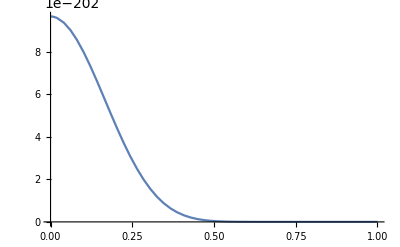

```mathematica
Plot[arg//.{τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),m->0,l->40,ω̄->0.4},{𝒥,0,1}]
```

## Relation with numerical ansatz

```mathematica
AllRelationAntsatz=Flatten[{
Rnear[1]-𝒶[0]/rp x^(-1-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(-1-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒴, hole]]&,
Rnear[-1]-rp 𝒷[0] x^(1-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(-1-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒵, hole]]&,
(Rfar[1]/.{r->rp x,ω->ω̄/rp})-fp/rp x^(-1-(ⅈ χ)/τ)//First@Solve[Coefficient[x^(1+(ⅈ χ)/τ)#,x,0]==0,Subscript[𝒴, in]]&,
(Rfar[-1]/.{r->rp x,ω->ω̄/rp})-rp fm x^(1-(ⅈ χ)/τ)//First@Solve[Coefficient[x^(-1+(ⅈ χ)/τ)#,x,0]==0,Subscript[𝒵, out]]&}
]/.{x^(Complex[0,-1] β_)->ⅇ^(ⅈ β HoldForm@Log[x])}
```

{𝒴_hole→rp τ 𝒶[0],𝒵_hole→𝒷[0]/(rp τ),𝒴_in→ⅇ^((ⅈ χ Log[x])/τ+ⅈ x ω̄) fp,𝒵_out→ⅇ^((ⅈ χ Log[x])/τ-ⅈ x ω̄) fm}

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,1/4 Abs[Subscript[𝒴, in]]^2}/.AllRelationAntsatz//Simplify[ComplexExpand@#,x>0]&
```

fm^2/fp^2

```mathematica
First@Solve[HoleRelation==0/.AllRelationAntsatz,𝒷[0]]//Factor@*FullSimplify
```

{𝒷[0]→(ℬ τ^2 𝒶[0])/(2 (-ⅈ τ-2 χ) χ)}

```mathematica
Divide@@{(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2,1/4 Abs[Subscript[𝒴, in]]^2}/.AllRelationAntsatz//Simplify[ComplexExpand@#,x>0]&
```

(τ^2 ω̄ 𝒶[0]^2)/(fp^2 χ)

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2}/.AllRelationAntsatz//Simplify[ComplexExpand@#,x>0]&
```

(fm^2 χ)/(τ^2 ω̄ 𝒶[0]^2)

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2}/.First@Solve[HoleRelation==0,Subscript[𝒴, hole]]/.AllRelationAntsatz//Factor@FullSimplify[ComplexExpand@#,x>0]&
```

(fm^2 ℬ^2 τ^2)/(4 χ (τ^2+4 χ^2) ω̄ 𝒷[0]^2)

## Experiments

```mathematica
testϕ2=2Pi ϵR Exp[-I ω t](bin Exp[-I ω r]/(ω r)^3+bout Exp[I ω r]/(ω r));
```

```mathematica
testϕ0=4Pi ϵR Exp[-I ω t](ain Exp[-I ω r]/(ω r)+aout Exp[I ω r]/(ω r)^3);
```

```mathematica
r^2(D[#1, r]-ⅈ ω #1&)@*(D[#1, r]-ⅈ ω#1&)@(2 r^2 testϕ2)-𝒿(𝒿+1) r^2 testϕ0 //Coefficient[Expand@#,Exp[-I ω r]r]&//bin/ain/.Simplify@First@Solve[#==0,bin]&
```

-1/4 𝒿 (1+𝒿)

```mathematica
(D[#, r]+I ω#&)@*(D[#, r]+I ω#&)@(r^2 testϕ0)-2𝒿(𝒿+1)testϕ2 //Coefficient[Expand@#,Exp[I ω r] r^-1]&//(bout/aout/.Simplify@First@Solve[#==0,bout])&//Factor
```

-4/(𝒿 (1+𝒿))

```mathematica
Table[{ℓ,Gamma[-2 l-1]/Gamma[-l]}/.l->ℓ+ϵ,{ℓ,0,20}]//Limit[#,ϵ->0]&//FindSequenceFunction[#,ℓ]&//Simplify
```

((-1)^(1+ℓ) 2^(-1-2 ℓ))/Pochhammer[3/2,ℓ]